```mathematica
PIDTune[TransferFunctionModel[{{{1.}},1+1.2s+3 s^2},s],"PI","ReferenceOutput"]
```

(10.2728 (0.320713+1. s))/(10.2728 (0.320713+1. s)+s (5.+6. s+15. s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1110.272834779549310.27283477954931FalseFalseFalseAutomaticNoneNoneAutomatic

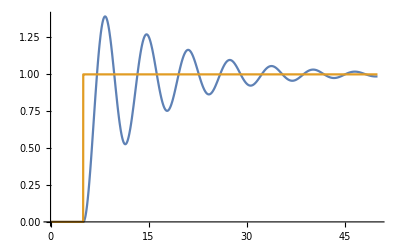

```mathematica
Plot[Evaluate@{OutputResponse[%, UnitStep[t-5],{t,0,50}],UnitStep[t-5]},{t,0,50},PlotRange->All,Exclusions->None]
```